0.+0.900316 (0.+x)-0.335749 (-0.785398+x) (0.+x)-0.0590239 (-1.5708+x) (-0.785398+x) (0.+x)+0.0375758 (-2.35619+x) (-1.5708+x) (-0.785398+x) (0.+x)-0.00280258 (-3.14159+x) (-2.35619+x) (-1.5708+x) (-0.785398+x) (0.+x)-0.000841068 (-3.92699+x) (-3.14159+x) (-2.35619+x) (-1.5708+x) (-0.785398+x) (0.+x)+0.000152983 (-4.71239+x) (-3.92699+x) (-3.14159+x) (-2.35619+x) (-1.5708+x) (-0.785398+x) (0.+x)+1.42359×10^-19 (-5.49779+x) (-4.71239+x) (-3.92699+x) (-3.14159+x) (-2.35619+x) (-1.5708+x) (-0.785398+x) (0.+x)

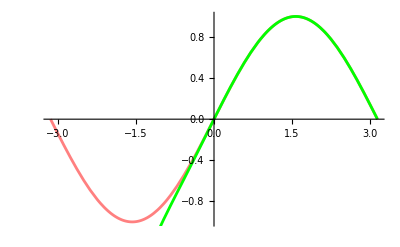

```mathematica
(*Newton's Divided Difference Interpolation*)
f[x_]:=Sin[x];
a= -N[Pi];
b=N[Pi];
n=8;
h = (b - a)/n;
Do[
x[i] = h*i,
{i, 0, n}
];
Do[
f[i, i + 1] = (f[x[i + 1]] - f[x[i]])/h,
{i, 0, n - 1}
];
Do[
f[i, i + k] = (f[i + 1, i + k] - f[i, i + k - 1])/(x[i + k] - x[i]),
{k, 2, n},
{i, 0, n-1}
];
p[x_]=f[x[0]] + Sum[
f[0, k]* Product[
(x - x[i]), 
{i, 0, k - 1}], 
{k, 1 , n}
]
fPlot = Plot[f[x], {x, -Pi, Pi}, PlotStyle->Pink];
pPlot = Plot[p[x], {x, -Pi, Pi}, PlotStyle-> Green];
Show[fPlot, pPlot]
```

```mathematica
(*Get digits of an integer a in base g:
IntegerDigits[a, g]*)
```

```mathematica
IntegerDigits[23]
```

{2,3}

```mathematica
IntegerDigits[23, 2]
```

```mathematica
{1,0,1,1,1}
```

{1,0,1,1,1}

```mathematica
(*Get digits of a real number a in base g:
RealDigits[a]*)
```

```mathematica
RealDigits[4.13]
```

{{4,1,3,0,0,0,0,0,0,0,0,0,0,0,0,0},1}

```mathematica
RealDigits[4.13, 2]
```

{{1,0,0,0,0,1,0,0,0,0,1,0,1,0,0,0,1,1,1,1,0,1,0,1,1,1,0,0,0,0,1,0,1,0,0,0,1,1,1,1,0,1,0,1,1,1,0,0,0,0,1,0,1},3}

```mathematica
(*Number a in base g:
BaseForm[a, g]*)
```

```mathematica
BaseForm[45.12, 2]
```

101101.0001111010111_2

```mathematica
(*Factorial of a:
a!*)
```

```mathematica
5!
```

120

```mathematica
(*Logarithm of a in base g:
Log[g, a]*)
```

```mathematica
Log[E]
```

1

```mathematica
Log[2, 4]
```

2

```mathematica
(*Trigonometric Functions*)
```

```mathematica
Tan[Pi]
```

0

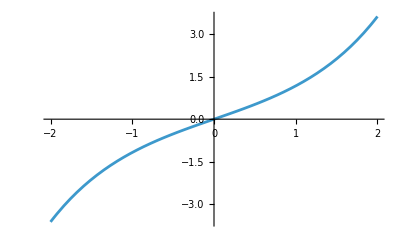

```mathematica
Plot[Sinh[x], {x, -2, 2}]
```

```mathematica
(*Floor and ceiling of a number a:
Floor[a], Ceiling[a]*)
```

```mathematica
Floor[3.5]
```

3

```mathematica
Ceiling[3.5]
```

4

```mathematica
(*Absolute value of a number a:
Abs[a]*)
```

```mathematica
Abs[-3.4]
```

3.4

```mathematica
Abs[3+4I]
```

5

```mathematica
(*Expand a polynomial p(x):
Expand[p(x)]*)
```

```mathematica
Expand[Power[ x+ x/y , 3]]
```

x^3+x^3/y^3+(3 x^3)/y^2+(3 x^3)/y

```mathematica
Plot3D[x^3+x^3/y^3+(3 x^3)/y^2+(3 x^3)/y,{x,-8,8},{y,-8,8}]
```

-Graphics3D-

```mathematica
Plot3D[x^3-x^3/y^3+(3 x^3)/y^2-(3 x^3)/y,{x,-8,8},{y,-8,8}]
```

-Graphics3D-

```mathematica
(*Factorize a polynomial p(x):
Factor[p(x)]*)
```

```mathematica
Factor[x^3-x^3/y^3+(3 x^3)/y^2-(3 x^3)/y]
```

(x^3 (-1+y)^3)/y^3

```mathematica
(*Simplify a polynomial p(x):
Simplify[p(x)]*)
```

```mathematica
Simplify[1/(x + 1)+1/(1 - x)+ 2/(1 + x^2 )]
```

-4/(-1+x^4)

```mathematica
(*Solve a system of equations with expressions e1, e2, ... and variables x1, x2, ...:
Solve[{e1, e2, ...}, {x1, x2, ...}]*)
```

```mathematica
Solve[{
x+ y + d== 1,
x - y == 3
},
{x, y}]
```

{{x→(4-d)/2,y→1/2 (-2-d)}}

```mathematica
(*Numerical approximation of a system of equations with expressions e1, e2, ... and variables x1, x2, ...:
NSolve[{e1, e2, ...}, {x1, x2, ...}]*)
```

```mathematica
NSolve[{
x - y == 1,
x + x y == 2
},
{x, y}]
```

{{x→-1.41421,y→-2.41421},{x→1.41421,y→0.414214}}

```mathematica
(*Check equality*)
```

```mathematica
s = Solve[{
x + y^2 == 1,
x - y == 3
},
{x, y}]
```

{{x→1/2 (5-ⅈ √7),y→1/2 (-1-ⅈ √7)},{x→1/2 (5+ⅈ √7),y→1/2 (-1+ⅈ √7)}}

```mathematica
ns = NSolve[{
x + y^2 == 1,
x - y == 3
},
{x, y}]
```

{{x→2.5-1.32288 ⅈ,y→-0.5-1.32288 ⅈ},{x→2.5+1.32288 ⅈ,y→-0.5+1.32288 ⅈ}}

```mathematica
Abs[s[[1]][[1]][[2]]] == Abs[ns[[1]][[1]][[2]]]
```

True

```mathematica
(*Sum of an expression e with respect to i in range a and b:
Sum[e, {i, a, b}]*)
```

```mathematica
Sum[i^2, {i, 0, 3}]
```

```mathematica
14
```

14

```mathematica
NSum[(i/j + j)^2, {i, 0, 3}, {j, 1, 4}]
```

187.931

```mathematica
(*Product of an expression e with respect to i in range a and b:
Product[e, {i, a, b}]*)
```

```mathematica
Product[i + 1, {i, 0, 4}]
```

```mathematica
120 (*5!*)
```

```mathematica
(*Legendre polynomial*)
```

```mathematica
pl1 = LegendreP[30, x];
```

```mathematica
pl2 = LegendreP[15, x];
```

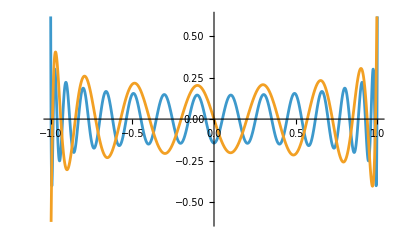

```mathematica
Plot[{pl1, pl2}, {x, -1, 1}]
```

```mathematica
sol = NSolve[LegendreP[100, x] == 0, x, 100];
A = x/.sol;
Table[{A[[i]], LegendreP[100, A[[i]]]}, {i, 1, 100}]
```

{{-0.9997137267734412336782284693423006767183495273084032267341983193325778326290650237421481532273003931,-4.77278625468272807268740061359237007399558450093015085313704431486911024600316947365728121363118846×10^-113},{-0.9984919506395958184001633591863491623048548504205697015727316216977961920518375362604142746344213709,1.5792029618934199031080479353513076702892458952842024114064946061997642252232541709916353844084496×10^-113},{-0.9962951347331251491861317322411310354364312881404303794500680496326332035836779589238386764235673233,-7.36295621269056485332208984385296073243729755996462857343516883560580551428651064512934768187703042×10^-114},{-0.9931249370374434596520098928487834707317714588665203786568877462750407581159503562095089992210807178,5.12006155992448736317888725578778097853136124312789604245106865144582590198002591415336237262489982×10^-114},{-0.9889843952429917480044187458077366318393336371069475277518151616689376352420307137266384824597719975,-2.64055186757658942381480128197805959795985683510461691874782753329704779868412863434196425297031821×10^-114},{-0.9838775407060570154961001555110081673443670168508022103488777183124296552679631925102451000606391964,1.94150287231014649969074656439817806214561194213143554025819823402215643937320258702213248991821012×10^-114},{-0.977809358486918288553781088429201928635234494266253978308576649096992608182694210635427696196825183,-3.59330976459996530109584883142090972206189717185957068943060414582228582894187726254235271767068175×10^-114},{-0.9707857757637063319308978578975053885505571994782071362917096707470703876956189039063625696575759283,1.58253176663278391703244819591121186807883753763169375130406426952964466026759191407411077375631678×10^-114},{-0.9628136542558155272936593260301663864373315067304141409782340260220288474962667532341593843360900971,-1.05262203920429629501305536623997605778978960717969396760986651242165108158788092067465014513637898×10^-114},{-0.953900782925491742849336930894357644645221451014667747667032915183023761430639133783370678271809278,7.74621859619571888894222795156084945091460557078390176164183818115420154912107241624678440138822481×10^-115},{-0.9440558701362559779627747064152187467397203733820968716296342860565033383282882070704096369368030732,-1.26494580095832529127209901276359516004482409204670916107647206535456531684834237134064795218952893×10^-114},{-0.9332885350430795459243336681308625040835460742970192958479582428963379615258971497696424273370505945,1.23525646139102462654096155371580096354306079543394856199003993295292900429073547357802961476260542×10^-114},{-0.921609298145333952666951328481987459124582797732196146614931921218195795972266744371780033114967928,-1.30992964878756872268291334465419242747173817782361915969227832656916579042047403461734240283638273×10^-114},{-0.9090295709825296904671263377891460644432772895845889380851263193192159125920984592060315629153469585,8.66388909191228488972284032212903370642365292063286573340428590993205120999255834709135119458404239×10^-115},{-0.8955616449707269866985210224302277698481817689977198299793548057692769962437911552698744788030984065,-2.53708901756932953156992831862968588287795443781772392193147313250346670946822580880556701648255447×10^-115},{-0.8812186793850184155733168254278055824454944110212578029408939879511744591614876202521308480717242079,3.15786611761288888503916609871992817336936882153908190282959953726495324476364276202395043540913695×10^-115},{-0.866014688497164623410739969676242966380314839305593072136282353093368594223154778449006270143043096,-2.88796303063742829657428010737634456880788430687762191113476196997735040333085278236378373152801413×10^-115},{-0.849964527879591284293362591420104654073790779500672354335728252552564403093558318913116900675984557,3.3737885871932573558110748917947950570185564332682498961854695910950355179098747457520837985140352×10^-115},{-0.8330838798884008235429158338447556799074948303099622593030660749580722045905811466768898021101509485,-3.50874013068098765004351788746658685929929869059897989203288837473883693862626973558216715045459661×10^-115},{-0.8153892383391762543939887586492580053825503765137027228998074603374444991349615573421689326973193174,3.94058506984172459158733547361632062659767391405731587874462848239900148491873370303843387666439311×10^-115},{-0.7968978923903144763895728821832459828895268559642905021897691851365429763910044811231931710394288482,-1.52945082619427666796768728428030709251507891641493995293741288129641610145247655140761132199302929×10^-115},{-0.7776279096494954756275513868344901065385397999360788750187363662040855456913062714844076284876271001,3.6706819828662640031224494822727370220361893993958558870497909151113986434859437233782671727832703×10^-115},{-0.7575981185197071760356679644384007723131089719000417126757861027246415776803142458827293725161663049,-1.92530868709161886438285340491756304587192287125174794075650797998490026888723518824252248768534275×10^-115},{-0.7368280898020207055124277148201010028432784462471234422373717288244021286511974338307776840740360038,1.52945082619427666796768728428030709251507891641493995293741288129641610145247655140761132199302929×10^-115},{-0.7153381175730564464599671227043659640843978385956296346372452971369782354108232474292371653548766714,-1.76336683490634251130392181011141288313503216245487194573960543961233856402756120044642246535666906×10^-115},{-0.6931491993558019659486479416754372655870000179307284537746534276660764537334055038847105985280413383,1.20556712182372396180982409466800676704129749882118796290360780055129269173312857581541127733568191×10^-115},{-0.6702830156031410158025870143232266136698056840288239544064363680107923867493729305934316748132479432,-1.29553481748221082463145275844920130189512567037500796013522032298049363887739190236880017862938952×10^-115},{-0.646761908514129279832630304458630435019733784248528000988170844528331185516142757842263720433434059,-2.58662127497814417076324335349432811789129781259147223232096360954012496741666576248502818225814099×10^-103},{-0.6226088602037077716041908451723122446538177322898160020859831756806700397503779098756461196502699432,-9.26667265282414687062775236946303708994430167004345971485608981020769755585912263499905683325188334×10^-116},{-0.5978474702471787212648065451493406363948991923204853355890654525451582770076902489802047093006648909,-1.31488405462883115135531602348393317057713388233102843805022677171531317720249627135357954129283355×10^-108},{-0.5725019326213811913168704435257254489600339496755602780428623902594241338059698242656458828776935556,4.49624984950636724782667594086819899637932723518002771304631995630280241873743295893033314605768058×10^-111},{-0.5465970120650941674679942571817499039562417759375278116220253290758369379749835263165961965771202774,-5.2972979203717064829374957234367342121934027410889214369973453206313517678542246674635385081735038×10^-114},{-0.5201580198817630566468157494552085307689376904200938534085213700592361814744223119830962098587247069,-3.81463029591984298363705534432264827780231447388196788262037095099812015891676504586368941485320246×10^-115},{-0.4932107892081909335693087934493339909907233253585561269111100309690047915688200485712105903959123146,-1.16958004356032921668117262915552895309976623019965996401096279157961231287542324519405571681819887×10^-116},{-0.4657816497733580422492166233957545816116511102122109663384736171841696259032634189377981612393939185,-2.69903086975460588464885991343583604561484514661459991694837567287602841432789979660166703881122816×10^-116},{-0.437897402172031513108978043622195962125701763484104595188310204051123144653702500742791038769342534,1.39449928270654637373524428860851529023433665908420995708999409765261468073608156157752797005246788×10^-115},{-0.4095852916783015425288684000571577014953643891647545593418332406033996575331830345806795628690573659,-1.39449928270654637373524428860851529023433665908420995708999409765261468073608156157752797005246788×10^-115},{-0.3808729816246299567633625488695874037497072651237109236688918529896939039271541471044500577579629244,5.75793252214315922058423448199645023064500297944447982282320143546886061723285289941688968279728674×10^-116},{-0.3517885263724217209723438295489705652493180963890712011764841982771959211583833760021494408968950459,-5.66796482648467235776260581821525569579117480789065982559158891303965967008858957286350078150357913×10^-116},{-0.3223603439005291517224765823983254274021916230230857071396235464838001687978675705153955347777724845,-5.57799713082618549494097715443406116093734663633683982835997639061045872294432624631011188020987153×10^-116},{-0.2926171880384719647375558882354943845615389891725809720966616591479275866303588261908855309923018198,8.81683417453171255651960905055706441567516081227435972869802719806169282013780600223211232678334532×10^-116},{-0.2625881203715034791689293362549821411320226945355221356619685263436360323364923325565206911409614645,1.13359296529693447155252116364305113915823496157813196511831778260793193401771791457270015630071583×10^-115},{-0.2323024818449739696495099632079641106975097715071369137590139207136369395991049910708324172849434974,-1.7093862175112503936109446118426961622227352595225799474006379261548179957410032045143891245804445×10^-115},{-0.2017898640957359972360488595303964629436920035590489112762105422926673150875882870548710970004739983,3.50874013068098765004351788746658685929929869059897989203288837473883693862626973558216715045459661×10^-116},{-0.171080080538603274887532374707089807465859725118066774687333733822605616907970579199403706186237367,-7.82718952228835706548169374896392453228305092518233975915028945134048240155090941014483441255256166×10^-116},{-0.1402031372361139732075146046824055166168730062633597720335909281997729861743816299481443939747092199,3.3288047393640139244002605599041977895916423474913398975696633298804350443377430824753893478671814×10^-116},{-0.1091892035800611150034260065793848868848996299691633933769594518624506698178425847120060261262350542,3.05890165238855333593537456856061418503015783282987990587482576259283220290495310281522264398605858×10^-116},{-0.07806858281343663669481737120155257397635002744853011605522973317573642901924147065894904079184899205,-3.86861091331493510133003254259136499871461137681425988095933846445564072720332304179572275562942703×10^-116},{-0.04687168242159163161492391293384830953706539908602407963127262211945011420530713241730850025934000927,-7.73722182662987020266006508518272999742922275362851976191867692891128145440664608359144551125885405×10^-116},{-0.01562898442154308287221669999742934014775618285556147271379873087358649059170425905638274318541429531,-5.84790021780164608340586314577764476549883115099829982005481395789806156437711622597027858409099434×10^-116},{0.01562898442154308287221669999742934014775618285556147271379873087358649059170425905638274318541429531,-5.84790021780164608340586314577764476549883115099829982005481395789806156437711622597027858409099434×10^-116},{0.04687168242159163161492391293384830953706539908602407963127262211945011420530713241730850025934000927,-7.73722182662987020266006508518272999742922275362851976191867692891128145440664608359144551125885405×10^-116},{0.07806858281343663669481737120155257397635002744853011605522973317573642901924147065894904079184899205,-3.86861091331493510133003254259136499871461137681425988095933846445564072720332304179572275562942703×10^-116},{0.1091892035800611150034260065793848868848996299691633933769594518624506698178425847120060261262350542,3.05890165238855333593537456856061418503015783282987990587482576259283220290495310281522264398605858×10^-116},{0.1402031372361139732075146046824055166168730062633597720335909281997729861743816299481443939747092199,3.3288047393640139244002605599041977895916423474913398975696633298804350443377430824753893478671814×10^-116},{0.171080080538603274887532374707089807465859725118066774687333733822605616907970579199403706186237367,-7.82718952228835706548169374896392453228305092518233975915028945134048240155090941014483441255256166×10^-116},{0.2017898640957359972360488595303964629436920035590489112762105422926673150875882870548710970004739983,3.50874013068098765004351788746658685929929869059897989203288837473883693862626973558216715045459661×10^-116},{0.2323024818449739696495099632079641106975097715071369137590139207136369395991049910708324172849434974,-1.7093862175112503936109446118426961622227352595225799474006379261548179957410032045143891245804445×10^-115},{0.2625881203715034791689293362549821411320226945355221356619685263436360323364923325565206911409614645,1.13359296529693447155252116364305113915823496157813196511831778260793193401771791457270015630071583×10^-115},{0.2926171880384719647375558882354943845615389891725809720966616591479275866303588261908855309923018198,8.81683417453171255651960905055706441567516081227435972869802719806169282013780600223211232678334532×10^-116},{0.3223603439005291517224765823983254274021916230230857071396235464838001687978675705153955347777724845,-5.57799713082618549494097715443406116093734663633683982835997639061045872294432624631011188020987153×10^-116},{0.3517885263724217209723438295489705652493180963890712011764841982771959211583833760021494408968950459,-5.66796482648467235776260581821525569579117480789065982559158891303965967008858957286350078150357913×10^-116},{0.3808729816246299567633625488695874037497072651237109236688918529896939039271541471044500577579629244,5.75793252214315922058423448199645023064500297944447982282320143546886061723285289941688968279728674×10^-116},{0.4095852916783015425288684000571577014953643891647545593418332406033996575331830345806795628690573659,-1.39449928270654637373524428860851529023433665908420995708999409765261468073608156157752797005246788×10^-115},{0.437897402172031513108978043622195962125701763484104595188310204051123144653702500742791038769342534,1.39449928270654637373524428860851529023433665908420995708999409765261468073608156157752797005246788×10^-115},{0.4657816497733580422492166233957545816116511102122109663384736171841696259032634189377981612393939185,-5.1281586525337511808328338355280884866682057785677398422019137784644539872230096135431673737413335×10^-115},{0.4932107892081909335693087934493339909907233253585561269111100309690047915688200485712105903959123146,-1.16958004356032921668117262915552895309976623019965996401096279157961231287542324519405571681819887×10^-116},{0.5201580198817630566468157494552085307689376904200938534085213700592361814744223119830962098587247069,-1.7093862175112503936109446118426961622227352595225799474006379261548179957410032045143891245804445×10^-115},{0.5465970120650941674679942571817499039562417759375278116220253290758369379749835263165961965771202774,-3.43856532806736789704264752971725512211331271678700029419223060724406019985374434087052380744550467×10^-114},{0.5725019326213811913168704435257254489600339496755602780428623902594241338059698242656458828776935556,1.70237013118750280086129782671662384903342941538559179681603099668248099695292988810315042013469845×10^-104},{0.5978474702471787212648065451493406363948991923204853355890654525451582770076902489802047093006648909,-3.20871211474357235368271998330407275115221188777280089527662215522875411674616024995227469037426864×10^-108},{0.6226088602037077716041908451723122446538177322898160020859831756806700397503779098756461196502699432,3.61430482578711415724473956041652287296725388947191097346496709823616395479356521269143650019994223×10^-108},{0.646761908514129279832630304458630435019733784248528000988170844528331185516142757842263720433434059,-7.20755728277689439277089643160620526266370710474230125465126945112633858445621865498023810592575237×10^-104},{0.6702830156031410158025870143232266136698056840288239544064363680107923867493729305934316748132479432,2.36755765157309696851630647415725158173864607104022614673708750278316402603981847619925135607753466×10^-102},{0.6931491993558019659486479416754372655870000179307284537746534276660764537334055038847105985280413383,-1.79868943771145583511452321953738796949358676152369753344194482623907074081676406768175113281063893×10^-103},{0.7153381175730564464599671227043659640843978385956296346372452971369782354108232474292371653548766714,-1.76336683490634251130392181011141288313503216245487194573960543961233856402756120044642246535666906×10^-115},{0.7368280898020207055124277148201010028432784462471234422373717288244021286511974338307776840740360038,1.52945082619427666796768728428030709251507891641493995293741288129641610145247655140761132199302929×10^-115},{0.7575981185197071760356679644384007723131089719000417126757861027246415776803142458827293725161663049,-1.92530868709161886438285340491756304587192287125174794075650797998490026888723518824252248768534275×10^-115},{0.7776279096494954756275513868344901065385397999360788750187363662040855456913062714844076284876271001,3.6706819828662640031224494822727370220361893993958558870497909151113986434859437233782671727832703×10^-115},{0.7968978923903144763895728821832459828895268559642905021897691851365429763910044811231931710394288482,-1.52945082619427666796768728428030709251507891641493995293741288129641610145247655140761132199302929×10^-115},{0.8153892383391762543939887586492580053825503765137027228998074603374444991349615573421689326973193174,3.94058506984172459158733547361632062659767391405731587874462848239900148491873370303843387666439311×10^-115},{0.8330838798884008235429158338447556799074948303099622593030660749580722045905811466768898021101509485,-3.50874013068098765004351788746658685929929869059897989203288837473883693862626973558216715045459661×10^-115},{0.849964527879591284293362591420104654073790779500672354335728252552564403093558318913116900675984557,3.3737885871932573558110748917947950570185564332682498961854695910950355179098747457520837985140352×10^-115},{0.866014688497164623410739969676242966380314839305593072136282353093368594223154778449006270143043096,-2.88796303063742829657428010737634456880788430687762191113476196997735040333085278236378373152801413×10^-115},{0.8812186793850184155733168254278055824454944110212578029408939879511744591614876202521308480717242079,3.15786611761288888503916609871992817336936882153908190282959953726495324476364276202395043540913695×10^-115},{0.8955616449707269866985210224302277698481817689977198299793548057692769962437911552698744788030984065,-2.53708901756932953156992831862968588287795443781772392193147313250346670946822580880556701648255447×10^-115},{0.9090295709825296904671263377891460644432772895845889380851263193192159125920984592060315629153469585,8.66388909191228488972284032212903370642365292063286573340428590993205120999255834709135119458404239×10^-115},{0.921609298145333952666951328481987459124582797732196146614931921218195795972266744371780033114967928,-1.30992964878756872268291334465419242747173817782361915969227832656916579042047403461734240283638273×10^-114},{0.9332885350430795459243336681308625040835460742970192958479582428963379615258971497696424273370505945,1.23525646139102462654096155371580096354306079543394856199003993295292900429073547357802961476260542×10^-114},{0.9440558701362559779627747064152187467397203733820968716296342860565033383282882070704096369368030732,-1.26494580095832529127209901276359516004482409204670916107647206535456531684834237134064795218952893×10^-114},{0.953900782925491742849336930894357644645221451014667747667032915183023761430639133783370678271809278,7.74621859619571888894222795156084945091460557078390176164183818115420154912107241624678440138822481×10^-115},{0.9628136542558155272936593260301663864373315067304141409782340260220288474962667532341593843360900971,-1.05262203920429629501305536623997605778978960717969396760986651242165108158788092067465014513637898×10^-114},{0.9707857757637063319308978578975053885505571994782071362917096707470703876956189039063625696575759283,1.58253176663278391703244819591121186807883753763169375130406426952964466026759191407411077375631678×10^-114},{0.977809358486918288553781088429201928635234494266253978308576649096992608182694210635427696196825183,-3.59330976459996530109584883142090972206189717185957068943060414582228582894187726254235271767068175×10^-114},{0.9838775407060570154961001555110081673443670168508022103488777183124296552679631925102451000606391964,1.94150287231014649969074656439817806214561194213143554025819823402215643937320258702213248991821012×10^-114},{0.9889843952429917480044187458077366318393336371069475277518151616689376352420307137266384824597719975,-2.64055186757658942381480128197805959795985683510461691874782753329704779868412863434196425297031821×10^-114},{0.9931249370374434596520098928487834707317714588665203786568877462750407581159503562095089992210807178,5.12006155992448736317888725578778097853136124312789604245106865144582590198002591415336237262489982×10^-114},{0.9962951347331251491861317322411310354364312881404303794500680496326332035836779589238386764235673233,-7.36295621269056485332208984385296073243729755996462857343516883560580551428651064512934768187703042×10^-114},{0.9984919506395958184001633591863491623048548504205697015727316216977961920518375362604142746344213709,1.5792029618934199031080479353513076702892458952842024114064946061997642252232541709916353844084496×10^-113},{0.9997137267734412336782284693423006767183495273084032267341983193325778326290650237421481532273003931,-4.77278625468272807268740061359237007399558450093015085313704431486911024600316947365728121363118846×10^-113}}